# Perez, Saez, Weed Free Damped Motion (Extended)

## Background Stuff:

## Background Equations

5.1.1 Spring/Mass systems: Free Undamped Motion

(d^2 x)/dt^2+ω^2 x=0		(1)
(ω^2=k/m)		


5.1.2: Spring/Mass Systems: Free Damped Motion

(d^2 x)/dt^2+2λ dx/dt+ω^2 x=0		(2)
(2λ=β/m,  ω^2=k/m)	
or
m(d^2 x)/dt^2+β dx/dt+k x=0                  (3)

## Part 1: Free Undamped Motion

(a) Use DSolve in Mathematica to verify the solution we found to (1).

```mathematica
DSolve[{x''[t]+ω^2 x[t] == 0},x[t],t]
```

{{x[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

(b) A 4 ft spring measures 8 ft after a 8 lb mass is attached.  Find the equation of motion if the mass is released from equilibrium with downward velocity of 5 ft/s and there is no damping. (Remember that F=ks where s is displacement and F=ma.)

F = ks
8lb (Force) = k* displacement = k*4
k = 2lb/ft

F = ma
8 = m*32
1/4 = m

ω^2 = k/m= 2/(1/4)=8
λ=0

(d^2 x)/dt^2+8x=0

x(0) = 0 (hasn’t moved at all- it’s a 4 ft spring, but it hasn’t moved at all the instant you put the weight on- 0, measure of displacement rather than position)
x’(0) = 5 (velocity at time 0)

```mathematica
DSolve[{x''[t]+8x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→(5 Sin[2 √2 t])/(2 √2)}}

## Part 2: Free Damped Motion (Specific)

(a) Use DSolve in Mathematica to find a general solution to (2).

```mathematica
DSolve[x''[t] + 2 λ x'[t]+ω^2 x[t]==0, x[t],t]
```

{{x[t]→ⅇ^(t (-λ-√(λ^2-ω^2))) C[1]+ⅇ^(t (-λ+√(λ^2-ω^2))) C[2]}}

(b) A 4 ft spring measures 8 ft after a 8 lb mass is attached.  Find the equation of motion if the mass is released from equilibrium with downward velocity of 5 ft/s and damping is √2 times the instantaneous velocity.  (In other words, β=√2.)

2λ=β/m,  ω^2=k/m
2λ = Sqrt[2]/(1/4)
λ = 2√2
ω^2=2/(1/4)
ω^2=8
ω = 2√2

(d^2 x)/dt^2+2λ dx/dt+ω^2 x=0
(d^2 x)/dt^2+4 √2 dx/dt+8x=0

x(0) = 0 (hasn’t moved at all- it’s a 4 ft spring, but it hasn’t moved at all the instant you put the weight on- 0, measure of displacement rather than position)
x’(0) = 5 (velocity at time 0)

```mathematica
DSolve[{x''[t] + 4 Sqrt[2] x'[t] + 8 x[t]==0, x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→5 ⅇ^(-2 √2 t) t}}

## Part 3: Free Damped Motion (Extended)

(a) Plot both of your results from Part 1(b) and Part 2(b), explain the differences in the two graphs and describe the motion of the spring in each case.  Clearly label your graph.

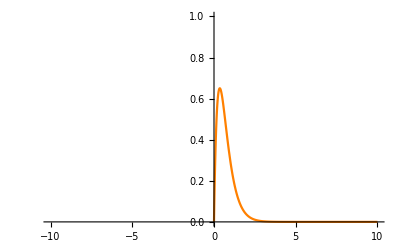

```mathematica
p1 =Plot[5 ⅇ^(-2 √2 t) t,{t,-10,10}, PlotRange-> {0,1}, PlotLegends->"5 ⅇ^(-2 SqrtBox[2] t) t", PlotStyle->Orange]
```

This graph is an example of a critcally damped harmonic oscillator because ω^2-λ^2=0.  Therefore the system is said to be critically damped because any slight decrease in the damping force would result in oscillatory motion.

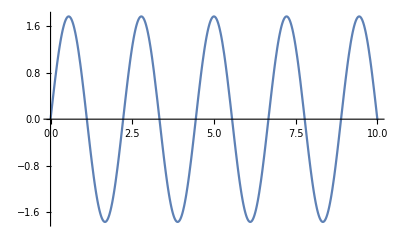

```mathematica
p2 = Plot[(5 Sin[2 √2 t])/(2 √2),{t,0,10}, PlotLegends->"(5 Sin[2 SqrtBox[2] t])/(2 SqrtBox[2])"]
```

This graph is an example of a harmonic oscillator with no damping.

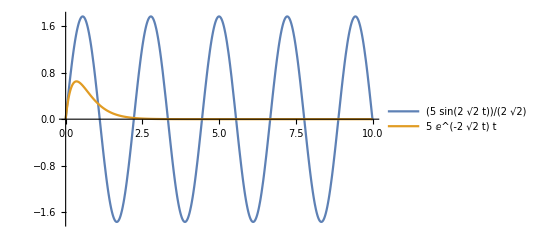

```mathematica
Plot[{(5 Sin[2 √2 t])/(2 √2),5 ⅇ^(-2 √2 t) t}, {t,0,10},PlotRange -> Automatic, PlotLegends->"Expressions"]
```

In the free damped situation, the system is said to be overdamped, critically damped, or underdamped in the following cases using the damped motion equation (2):
(d^2 x)/dt^2+2λ dx/dt+ω^2 x=0
Case 1 (overdamped): λ^2-ω^2>0
The system is said to be overdamped because the damping coefficient β is large when compared to the spring constant k.
Assume λ^2 = 100 (therefore, λ = 10) and ω^2 = 1 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *10 dx/dt+1x=0

```mathematica
DSolve[{x''[t] + 20x'[t] +  x[t]==0, x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→(5 (10+3 √11) (ⅇ^(t/(-10-3 √11))-ⅇ^((-10-3 √11) t)))/(6 (33+10 √11))}}

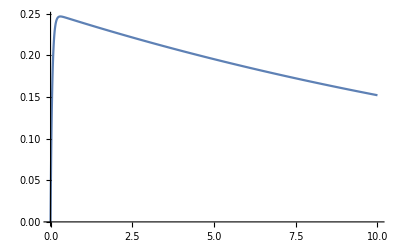

```mathematica
f1 =Plot[(5 (10+3 √11) (ⅇ^(t/(-10-3 √11))-ⅇ^((-10-3 √11) t)))/(6 (33+10 √11)),{t,0,10},PlotRange->All, PlotLegends->"5/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))"]
```

Assume λ^2 = 81(therefore, λ = 9) and ω^2 = 1 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *9 dx/dt+1x=0

```mathematica
DSolve[{x''[t]+18x'[t]+x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→(5 (9+4 √5) (ⅇ^(t/(-9-4 √5))-ⅇ^((-9-4 √5) t)))/(8 (20+9 √5))}}

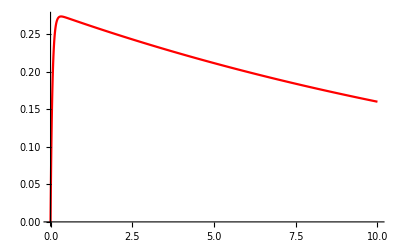

```mathematica
f2 =Plot[(5 (9+4 √5) (ⅇ^(t/(-9-4 √5))-ⅇ^((-9-4 √5) t)))/(8 (20+9 √5)),{t,0,10},PlotRange->All, PlotLegends->"(5 (9 + 4 SqrtBox[5]) (SuperscriptBox[ⅇ, FractionBox[t, -9 - 4 SqrtBox[5]]] - SuperscriptBox[ⅇ, (-9 - 4 SqrtBox[5]) t]))/(8 (20 + 9 SqrtBox[5]))", PlotStyle->Red]
```

Assume λ^2 = 125(therefore, λ = 25) and ω^2 = 1 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *25 dx/dt+1x=0

```mathematica
DSolve[{x''[t]+50x'[t]+x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→(5 (25+4 √39) (ⅇ^(t/(-25-4 √39))-ⅇ^((-25-4 √39) t)))/(8 (156+25 √39))}}

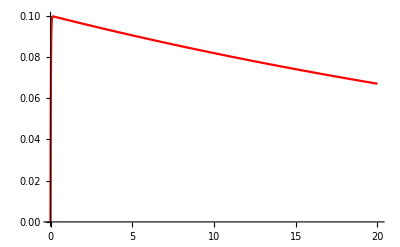

```mathematica
f2 =Plot[(5 (25+4 √39) (ⅇ^(t/(-25-4 √39))-ⅇ^((-25-4 √39) t)))/(8 (156+25 √39)),{t,0,20},PlotRange->All, PlotLegends->"(5 (9 + 4 SqrtBox[5]) (SuperscriptBox[ⅇ, FractionBox[t, -9 - 4 SqrtBox[5]]] - SuperscriptBox[ⅇ, (-9 - 4 SqrtBox[5]) t]))/(8 (20 + 9 SqrtBox[5]))", PlotStyle->Red]
```

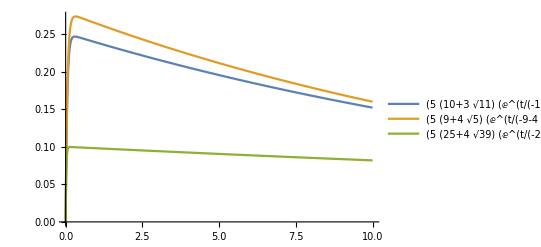

```mathematica
Plot[{(5 (10+3 √11) (ⅇ^(t/(-10-3 √11))-ⅇ^((-10-3 √11) t)))/(6 (33+10 √11)),(5 (9+4 √5) (ⅇ^(t/(-9-4 √5))-ⅇ^((-9-4 √5) t)))/(8 (20+9 √5)),(5 (25+4 √39) (ⅇ^(t/(-25-4 √39))-ⅇ^((-25-4 √39) t)))/(8 (156+25 √39))}, {t,0,10},PlotRange -> All, PlotLegends->"Expressions"]
```

For overdamped, the values must be significantly different in magnitude in order for the graph to clearly that the function does not go to zero over a relatively small t domain.

Case 2 (critically damped): λ^2-ω^2=0
The system is said to be critically damped because any slight decrease in the damping force would result in oscillatory motion.
Assume λ^2 = 4(therefore, λ = 2) and ω^2 = 4 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *2 dx/dt+4x=0

```mathematica
DSolve[{x''[t]+4x'[t]+4x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→5 ⅇ^(-2 t) t}}

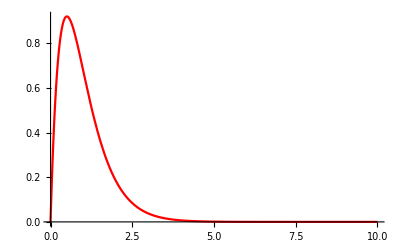

```mathematica
g1 = Plot[5 ⅇ^(-2 t) t,{t,0,10},PlotRange->All, PlotLegends->"5 ⅇ^(-2 t) t", PlotStyle->Red]
```

Assume λ^2 = 16(therefore, λ = 4) and ω^2 = 16 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *4 dx/dt+16x=0

```mathematica
DSolve[{x''[t]+8x'[t]+16x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→5 ⅇ^(-4 t) t}}

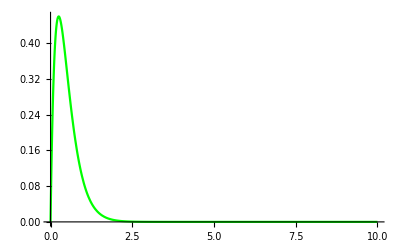

```mathematica
Plot[5 ⅇ^(-4 t) t,{t,0,10},PlotRange->All, PlotLegends->"5 ⅇ^(-4 t) t", PlotStyle->Green]
```

Assume λ^2 = 25(therefore, λ = 5) and ω^2 = 25 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *5 dx/dt+25x=0

```mathematica
DSolve[{x''[t]+10x'[t]+25x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→5 ⅇ^(-5 t) t}}

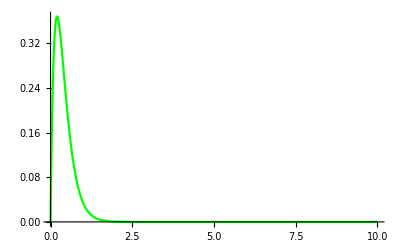

```mathematica
Plot[5 ⅇ^(-5t) t,{t,0,10},PlotRange->All, PlotLegends->"5 ⅇ^(-5 t) t", PlotStyle->Green]
```

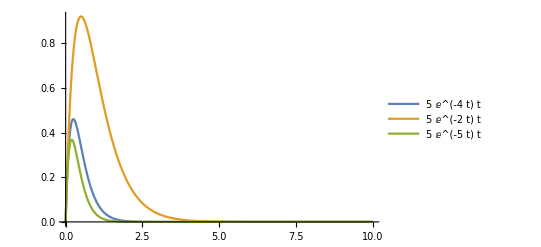

```mathematica
Plot[{5 ⅇ^(-4 t) t,5 ⅇ^(-2 t) t,5 ⅇ^(-5t) t}, {t,0,10},PlotRange -> All, PlotLegends->"Expressions"]
```

Case 3 (underdamped): λ^2-ω^2<0
The system is said to be underdamped because the damping coefficient β is small in comparison to the spring constant k.
Assume λ^2 = 4(therefore, λ = 2) and ω^2 = 16 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *2 dx/dt+16x=0

```mathematica
DSolve[{x''[t]+4x'[t]+16x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→(5 ⅇ^(-2 t) Sin[2 √3 t])/(2 √3)}}

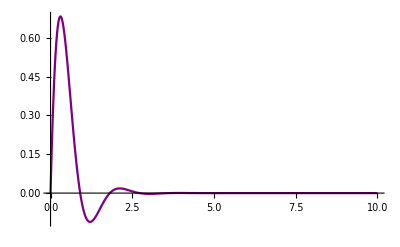

```mathematica
t1 = Plot[(5 ⅇ^(-2 t) Sin[2 √3 t])/(2 √3),{t,0,10},PlotRange->All, PlotLegends->"(5 SuperscriptBox[ⅇ, -2 t] Sin[2 SqrtBox[3] t])/(2 SqrtBox[3])", PlotStyle->Purple]
```

Assume λ^2 = 9(therefore, λ = 3) and ω^2 = 16 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *3 dx/dt+16x=0

```mathematica
DSolve[{x''[t]+6x'[t]+16x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→(5 ⅇ^(-3 t) Sin[√7 t])/(√7)}}

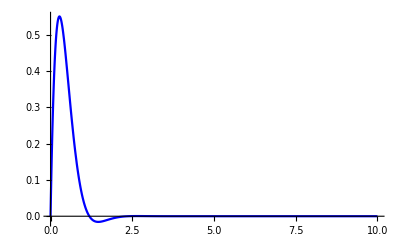

```mathematica
t2 = Plot[(5 ⅇ^(-3 t) Sin[√7 t])/(√7),{t,0,10},PlotRange->All, PlotLegends->"(5 SuperscriptBox[ⅇ, -3 t] Sin[SqrtBox[7] t])/(√7)", PlotStyle->Blue]
```

Assume λ^2 = 25(therefore, λ = 3) and ω^2 = 256 in the same system as above where x[0]=0 and x'[0]=5 .  The equation of this system is:
(d^2 x)/dt^2+2 *(5)dx/dt+256x=0

```mathematica
DSolve[{x''[t]+10x'[t]+256x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→(5 ⅇ^(-5 t) Sin[√231 t])/(√231)}}

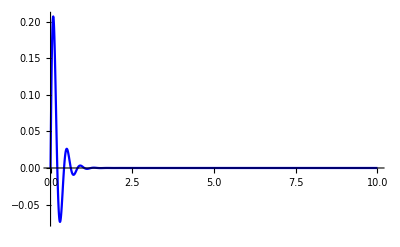

```mathematica
t2 = Plot[(5 ⅇ^(-5 t) Sin[√231 t])/(√231),{t,0,10},PlotRange->All, PlotLegends->"(5 SuperscriptBox[ⅇ, -5 t] Sin[SqrtBox[231] t])/(√231)", PlotStyle->Blue]
```

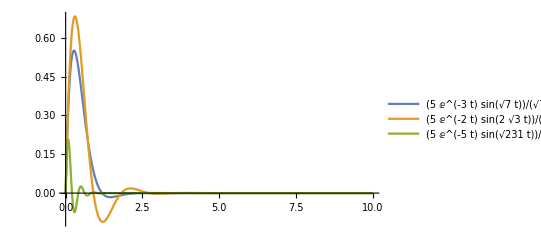

```mathematica
Plot[{(5 ⅇ^(-3 t) Sin[√7 t])/(√7),(5 ⅇ^(-2 t) Sin[2 √3 t])/(2 √3),(5 ⅇ^(-5 t) Sin[√231 t])/(√231)}, {t,0,10},PlotRange -> All, PlotLegends->"Expressions"]
```

(b) Using your result from Part 2(a), explain how the three cases above result in characteristically different solutions.

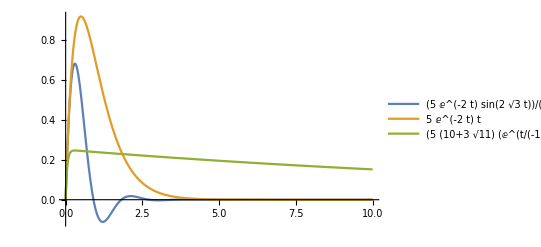

```mathematica
Plot[{(5 ⅇ^(-2 t) Sin[2 √3 t])/(2 √3),5 ⅇ^(-2 t) t,(5 (10+3 √11) (ⅇ^(t/(-10-3 √11))-ⅇ^((-10-3 √11) t)))/(6 (33+10 √11))}, {t,0,10},PlotRange -> All, PlotLegends->"Expressions"]
```

In the case of underdamping, because λ^2 is larger than ω^2, the second term dominates the function in a way that overpowers the oscillation of the first term. In the case of critical damping, the second and third term both overpower the first term , causing the whole function to go to zero with no oscillations.  Finally, when the oscillator is underdamped, these same last two terms eventually overpower the oscillatory motion caused by the first term. The only difference is how quickly the second and third term take the function to zero. When underdamped, the oscillator actually completes a couple of oscillations before going to zero (or stopping).

As a part of this explanation, create multiple, well labeled graphs that illustrate each of the three cases.  Use at least three curves (if not more) in each graph for each case.  (So you should have at least three graphs on each of three well-labeled plots/graphical images.)  Be clear with ANY values you are using.  If you use a problem from the book or the problems earlier in the lab as a starting point, say so and be clear with all steps.  Consider these graphs to be your explanation to a fellow undergraduate student of the differences in the cases.  Although you are creating graphs as a goal, you should have accompanying text that fully explains your process. Just because you have numbers in your Mathematica code (which I should see) you need to state all your choices.